Calculate the normalized array factor and the directivity for the specified problem.

```mathematica
ClearAll[ n, m, R, kd, x0, t4, max, af, theta, phi, u ]
n = 5 ;
m = n -1 ;
R = 10^2 ; (*40 = 20 log10(R)*)
kd = Pi ;
x0 = Cosh[(1/m) ArcCosh[R]] // N ;

t4[u_] = ChebyshevT[ m, x0 Cos[u/2]] // TrigReduce  ;

(*x-axis*)
max = NMaximize[ {t4[ kd Sin[theta] Cos[phi]],0 < theta < Pi, 0 < phi < 2 Pi},{theta, phi}] ;

(*z-axis*)
(*max = NMaximize[ {t4[ kd Cos[theta] ],0 < theta < Pi}, {theta}]*)

af[u_] = t4[u]/(max // First) // Simplify ;

prad = NIntegrate[ af[ kd Sin[t] Cos[p]]^2 Sin[t], {t, 0, Pi}, {p, 0, 2 Pi}] ;
directivity= 4 Pi/prad ;

TableForm[{
{"x_0 = ", x0},
{"AF(u) = ",
af[ kd u ] // TraditionalForm},
{"AF(θ, ϕ) = ",
af[ kd Sin[θ] Cos[ϕ]] // TraditionalForm},
{"D = ", directivity},
{"D (dB) = ",10 Log10[directivity]}
}]
max = 1 ;  (*now normalized*)
```

x_0 =  | 2.01325
AF(u) =  | 0.495 cos(3.14159 u)+0.164282 cos(6.28319 u)+0.340718
AF(θ, ϕ) =  | 0.495 cos(3.14159 sin(θ) cos(ϕ))+0.164282 cos(6.28319 sin(θ) cos(ϕ))+0.340718
D =  | 3.96675
D (dB) =  | 5.98435

Grab the magnitudes of the currents in the desired (polynomial) order for the Chebychev array.

```mathematica
ClearAll[ a, b, u, z ]
a = af[u] // TrigToExp ;
b = (a /. u -> -I Log[z] // Simplify ) z^2. // Simplify
```

0.0821408+0.2475 z^1.+0.340718 z^2.+0.2475 z^3.+0.0821408 z^4.

```mathematica
ClearAll[ linear, z, t, p, maxLin, pradlin, directivitylin ]
linear[z_] = (1 + z + z^2 + z^3 + z^4)/5 ;
lin[t_, p_] =linear[ E^(I  kd Sin[t] Cos[p])] ;


(*verify normalization*)
(*maxLin = NMaximize[ {Abs[lin[theta, phi]],0 < theta < Pi, 0 < phi < 2 Pi},{theta, phi}] ;
maxLin // First
*)

pradlin = NIntegrate[  Abs[lin[t, p]]^2  Sin[t], {t, 0, Pi}, {p, 0, 2 Pi}] ;
directivitylin= 4 Pi/pradlin 

TableForm[{

{"AF(θ, ϕ) = ",
lin[θ, ϕ] // TraditionalForm},
{"D = ", directivitylin},
{"D (dB) = ",10 Log10[directivitylin]}
}]
max = 1 ;  (*now normalized*)
```

5.+0. ⅈ

AF(θ, ϕ) =  | 1/5 (ⅇ^(ⅈ π sin(θ) cos(ϕ))+ⅇ^(2 ⅈ π sin(θ) cos(ϕ))+ⅇ^(3 ⅈ π sin(θ) cos(ϕ))+ⅇ^(4 ⅈ π sin(θ) cos(ϕ))+1)
D =  | 5.+0. ⅈ
D (dB) =  | 6.9897+0. ⅈ

Do the plots

```mathematica
ClearAll[ p1, q1, q2, t, i, asz, toff, axes ] ;

p1 = PolarPlot[ {af[ kd Sin[t] Cos[0]]^2, lin[t, 0] Conjugate[lin[t,0]]},
{t, 0, Pi},
PolarAxesOrigin->{0,1 },
PolarGridLines->Automatic,PolarAxes->True,PolarTicks->{Table[{N[Pi/6 i],ToString[30 i]<>"°"},{i,-5,6}],Automatic},
PlotLegends->Placed[ {"T_4(x_0cos(u/2))","∑_(n = 0)^4  e^(n TraditionalForm`ⅈ u)"}, {Right, Bottom}]
] 



asz = max /2 ;
toff = 0.1 ;
axes = Graphics3D[{
Red,Arrow[Tube[{{0,0,0},{asz,0,0}}] , 0.05],
Blue,Arrow[Tube[{{0,0,0},{0,asz,0}}] , 0.05],
Darker[Green, .8],Arrow[Tube[{{0,0,0},{0,0,asz}}] , 0.05],
Text[ "e_1",  {asz + toff,0,0} ],
Text[ "e_2",  {0,asz + toff,0} ],
Text[ "e_3",  {0,0,asz + toff} ]
}] ;

q1= Show[
SphericalPlot3D[ af[ kd Sin[t] Cos[p]]^2, {t, 0, Pi}, {p, 0, 2 Pi},
PlotRange -> {-max, max},
(*PerformanceGoal->perfgoal,*)
AxesLabel->{x,y,z}
],axes] 

q2= Show[
SphericalPlot3D[ lin[t, p] Conjugate[lin[t,p]], {t, 0, Pi}, {p, 0, 2 Pi},
PlotRange -> {-max, max},
(*PerformanceGoal->perfgoal,*)
AxesLabel->{x,y,z}
],axes]
```

-Graphics-

-Graphics3D-

-Graphics3D-

```mathematica
r1= Plot3D[ af[ kd Sin[t] Cos[p]]^2, {t, 0, Pi}, {p, 0, 2 Pi},
PlotRange -> {-max, max},
AxesLabel->{θ, ϕ, "|AF|^2"}
] 

r2= Plot3D[ Abs[ lin[t,p]]^2, {t, 0, Pi}, {p, 0, 2 Pi},
PlotRange -> {-max, max},
AxesLabel->{θ, ϕ, "|AF|^2"}
]
```

-Graphics3D-

-Graphics3D-

Visualize zeros for the Chebychev array factor (in the visible space domain).

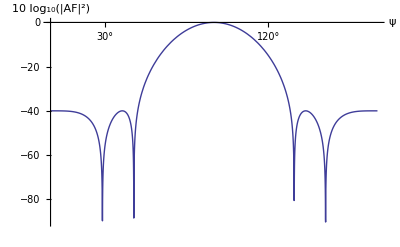

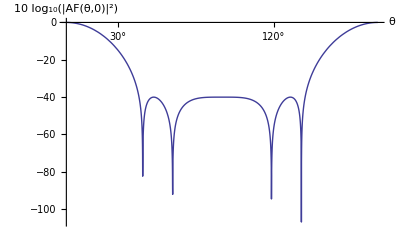

```mathematica
s1= Plot[ 10 Log10[af[ kd Cos[p]]^2], {p, 0,  Pi},
Ticks->{Table[{N[Pi/6 i],ToString[30 i]<>"°"},{i,-5,6}], Automatic},
AxesLabel->{ψ, "10 log_10(|AF|^2)"}
] 
s2= Plot[ 10 Log10[af[ kd Sin[t]Cos[0]]^2], {t, 0,  Pi},
Ticks->{Table[{N[Pi/6 i],ToString[30 i]<>"°"},{i,-5,6}], Automatic},
AxesLabel->{θ, "10 log_10(|AF(θ,0)|^2)"}
]
```

```mathematica
solutionTheta = Solve[ {af[ kd Sin[theta]Cos[0]]^2 == 0,0 < theta < Pi},theta]  ;
solutionPsi = Solve[ {af[ kd Cos[psi]]^2 == 0, 0 < psi < Pi}, psi] ;

(psi /. solutionPsi ) 180/Pi // DeleteDuplicates // TableForm
(theta /. solutionTheta ) 180/Pi // DeleteDuplicates // TableForm

(*-3 dB == 10^-0.3*)
solution3DbTheta = Solve[ {af[ kd Sin[theta]Cos[0]]^2 == 10^(-0.3),0 < theta < Pi},theta]  ;
solution3DbPsi = Solve[ {af[ kd Cos[psi]]^2 == 10^(-0.3), 0 < psi < Pi}, psi] ;

(psi /. solution3DbPsi ) 180/Pi // DeleteDuplicates // TableForm
(theta /. solution3DbTheta ) 180/Pi // DeleteDuplicates // TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

28.5682
45.8542
134.146
151.432

44.1458
61.4318
118.568
135.854

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

76.003
103.997

13.997
166.003

Zeros in visible domain for the linear uniform array.

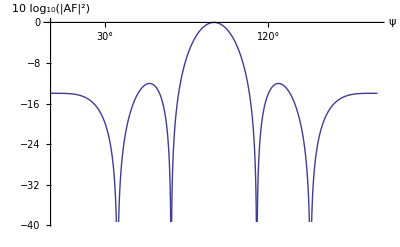

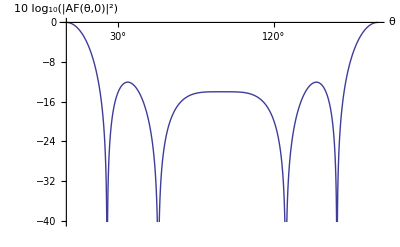

36.8699
66.4218
113.578
143.13

23.5782
53.1301
126.87
156.422

```mathematica
linearU[u_] = (1/n)Sin[ n u /2 ]/Sin[ u/2 ] ;

s3= Plot[ 10 Log10[linearU[ kd Cos[p]]^2], {p, 0,  Pi},
Ticks->{Table[{N[Pi/6 i],ToString[30 i]<>"°"},{i,-5,6}], Automatic},
AxesLabel->{ψ, "10 log_10(|AF|^2)"}
] 
s4= Plot[ 10 Log10[linearU[ kd Sin[t]Cos[0]]^2], {t, 0,  Pi},
Ticks->{Table[{N[Pi/6 i],ToString[30 i]<>"°"},{i,-5,6}], Automatic},
AxesLabel->{θ, "10 log_10(|AF(θ,0)|^2)"}
] 

solutionLinTheta = Solve[ {linearU[ kd Sin[theta]Cos[0]]^2 == 0,0 < theta < Pi},theta]  ;
solutionLinPsi = Solve[ {linearU[ kd Cos[psi]]^2 == 0, 0 < psi < Pi}, psi] ;

(psi /. solutionLinPsi ) 180/Pi // DeleteDuplicates // N// Sort // TableForm
(theta /. solutionLinTheta ) 180/Pi // DeleteDuplicates // N// Sort // TableForm
```

Save the plots for the report.

```mathematica
<<peeters` ;
(*peeters`setGitDir[ "notes\\blogit" ] *)
peeters`setGitDir[ "figures\\ece1229" ]
```

C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229

```mathematica
(*peeters`exportForLatex["chebychevVsLinearArrayBothBroadsideFig2", p1]*)
(*peeters`exportForLatex["chebychevBroadside3DFig3", q1]*)
(*peeters`exportForLatex["chebychevAndLinearZdomainZerosFig4", p3]*)
(*peeters`exportForLatex["chebychevDbPlotZXplaneFig5", s2]*)
peeters`exportForLatex["uniformDbPlotZXplaneFig6", s4]
```

{C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229/uniformDbPlotZXplaneFig6.eps,C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229/uniformDbPlotZXplaneFig6pn.png}

Where are the zeros located on the unit circle (in the z-domain)?

```mathematica
ClearAll[ zerosU, az, nn, zerosLin, azLin, p3 ]
zerosU[nn_] = 2 ArcCos[ Cos[Pi(2 nn - 1)/(2 m)]/x0] ;
(*all the zeros:*)

az = zerosU[#] &/@ (Range[ 2m]-m) ;
zerosPsiCheb = (180/Pi)ArcCos[#/kd] & /@ az ;
zerosThetaXYCheb = (180/Pi)ArcSin[#/kd] & /@ az ;

(*verify zeros*)
(*t4[#] &/@ az *)

zerosLin = 2 Pi # / n & ;
azLin = zerosLin[#] &/@ Range[m] ;
(*linear[ E^(I #) ] & /@ azLin // N*)
zerosPsiLin = (180/Pi)ArcCos[#/kd] & /@ azLin  // N;
zerosThetaXYLin = (180/Pi)ArcSin[#/kd] & /@ azLin  // N;


TableForm[
{
{"type", "zeros(u)", "(degrees)", "zeros(psi)", "zeros(theta,xy)"},
{"Chebychev", az, (180 #/Pi &/@ az), zerosPsiCheb, zerosThetaXYCheb },
{"Uniform", azLin, (180 #/Pi &/@ azLin), zerosPsiLin, zerosThetaXYLin}
} ]




p3 = ListPolarPlot[ {({#,1} &/@ az), ({#, 1} &/@ azLin) } // Evaluate,
PolarAxesOrigin->{0,1 },
PolarGridLines->Automatic,
PolarAxes->True,
PolarTicks->{Table[{N[Pi/6 i],ToString[30 i]<>"°"},{i,-5,6}],Automatic},
PlotStyle->PointSize[Large],
PlotLegends->Placed[ {"T_4(x_0cos(u/2))","∑_(n = 0)^4  e^(n TraditionalForm`ⅈ u)"}, {Right, Bottom}]
]
```

type | zeros(u) | (degrees) | zeros(psi) | zeros(theta,xy)
Chebychev | 4.09511
3.52409
2.7591
2.18808
2.18808
2.7591
3.52409
4.09511 | 234.632
201.915
158.085
125.368
125.368
158.085
201.915
234.632 | 0.+43.5819 ⅈ
0.+27.9939 ⅈ
28.5682
45.8542
45.8542
28.5682
0.+27.9939 ⅈ
0.+43.5819 ⅈ | 90.-43.5819 ⅈ
90.-27.9939 ⅈ
61.4318
44.1458
44.1458
61.4318
90.-27.9939 ⅈ
90.-43.5819 ⅈ
Uniform | (2 π)/5
(4 π)/5
(6 π)/5
(8 π)/5 | 72
144
216
288 | 66.4218
36.8699
0.+35.6587 ⅈ
0.+59.9868 ⅈ | 23.5782
53.1301
90.-35.6587 ⅈ
90.-59.9868 ⅈ

-Graphics-

```mathematica
134.14584861753974-45.85415138246025

44.14584861753976*2
```

88.2917

88.2917